Adapted from http://demonstrations.wolfram.com/MolecularDynamicsOfLennardJonesParticlesUsingTheVelocityVerl/

### Pergunta 5.3 a)

```mathematica
ClearAll["Global`*"]
SeedRandom[]
```

```mathematica
(* use natural units *)
ϵ=1.0;
σ=1.0;
m=1.0;
dt=0.002σ*Sqrt[m/ϵ];
kb=1;
```

```mathematica
pairForce:=
Function[{ii,jj,posk},
Module[{xii,xjj,r,vector,r6},
xii=posk[[ii,All]];
xjj=posk[[jj,All]];
r=Sqrt[(xjj[[1]]-xii[[1]])^2+(xjj[[2]]-xii[[2]])^2+(xjj[[3]]-xii[[3]])^2];
vector=(xii- xjj)/r;
(* Use this trick avoids enormous forces when particles get (artificially) too close. Therefore this is a modified Lennard-Jones Force:  r=Max[r,σ];*)
r6 = r^6;
4*ϵ*(12σ^12/(r6^2*r)-6σ^6/(r6*r))*vector ] ]

pairEnergy:=
Function[{ii,jj,posk},
Module[{xii,xjj,r,vector,r6},
xii=posk[[ii,All]];
xjj=posk[[jj,All]];
r=Sqrt[(xjj[[1]]-xii[[1]])^2+(xjj[[2]]-xii[[2]])^2+(xjj[[3]]-xii[[3]])^2];
(* Use this trick avoids enormous forces when particles get (artificially) too close. Therefore this is a modified Lennard-Jones Force:  r=Max[r,σ];*)
r6 = r^6;
4*ϵ*(σ^12/r6^2-σ^6/r6) ] ]

pairForceSum:=Function[{posk},
Module[{nat,forceTable,forcesum},
nat=Dimensions[posk][[1]];
forceTable=Table[{0.0,0.0,0.0},{i,1,nat},{j,1,nat}];
Do[forceTable[[i,j]]=pairForce[i,j,posk[[All,All]] ],{i,2,nat},{j,1,i-1}];Do[forceTable[[i,j]]=pairForce[i,j,posk[[All,All]] ],{i,1,nat-1},{j,i+1,nat}];
forcesum=Sum[forceTable[[All,i]],{i,1,nat}]
  ] ]

pairEnergySum:=Function[{posk},
Module[{nat,energysum},
nat=Dimensions[posk][[1]];
Sum[Sum[pairEnergy[i,j,posk ],{j,1,i-1}],{i,2,nat}]
  ] ]
```

```mathematica
(* define table sizes andinitialize tables with zeroes , storing all steps *)
natoms=13;
timesteps = 1000;
position = Table[0.0,{k,1,timesteps+1},{j,1,natoms},{i,1,3}];velocity = Table[0.0,{k,1,timesteps+1},{j,1,natoms},{i,1,3}];
force=Table[0.0,{k,1,timesteps+1},{j,1,natoms},{i,1,3}];
energy = Table[0.0,{k,1,timesteps+1}];
kinetic = Table[0.0,{k,1,timesteps+1}];
```

```mathematica
(* initialize positions to 13 atom cubo-octahedron*)
dfcc = 1.0/(√2.0) 2.0^(1/6) σ;
position[[1,1,1]]=0.1 dfcc(*0.1*);
position[[1,1,2]]=-0.1 dfcc(*-0.1*);
position[[1,1,3]]=-0.05 dfcc(*-0.05*);

position[[1,2,1]]=0.0;
position[[1,2,2]]=dfcc;
position[[1,2,3]]=dfcc;

position[[1,3,1]]=dfcc;
position[[1,3,2]]=0.0;
position[[1,3,3]]=dfcc;

position[[1,4,1]]=dfcc;
position[[1,4,2]]=dfcc;
position[[1,4,3]]=0.0;

position[[1,5,1]]=0.0;
position[[1,5,2]]=-dfcc;
position[[1,5,3]]=dfcc;

position[[1,6,1]]=-dfcc;
position[[1,6,2]]=0.0;
position[[1,6,3]]=dfcc;

position[[1,7,1]]=-dfcc;
position[[1,7,2]]=dfcc;
position[[1,7,3]]=0.0;

position[[1,8,1]]=0.0;
position[[1,8,2]]=dfcc;
position[[1,8,3]]=-dfcc;

position[[1,9,1]]=dfcc;
position[[1,9,2]]=0.0;
position[[1,9,3]]=-dfcc;

position[[1,10,1]]=dfcc;
position[[1,10,2]]=-dfcc;
position[[1,10,3]]=0.0;

position[[1,11,1]]=0.0;
position[[1,11,2]]=-dfcc;
position[[1,11,3]]=-dfcc;

position[[1,12,1]]=-dfcc;
position[[1,12,2]]=0.0;
position[[1,12,3]]=-dfcc;

(*quebra de simetria*)
position[[1,13,1]]=4/3 dfcc;(*-*)
position[[1,13,2]]=4/3 dfcc;(*-*)
position[[1,13,3]]=4/3 dfcc;
```

```mathematica
(* Plot of the first configuration *)
ListPointPlot3D[ position[[1,All,All]] ,BoxRatios->{1, 1, 1} ,PlotStyle->{PointSize[0.1]},PlotRangePadding->0.3,Axes->None,Boxed->False]
```

-Graphics3D-

```mathematica
(* Initialize velocities (by default they are zero) and calculate kinetic energy *)
Do[Do[velocity[[1,j,i]]=0.05RandomReal[],{i,1,3}],{j,1,13}]
```

```mathematica
Do[force[[k,All,All]]=pairForceSum[ position[[k,All,All]] ];    energy[[k]] =pairEnergySum[ position[[k,All,All]]  ] ;kinetic[[k]] = 0.5  m  Sum[velocity[[k,j,i]]^2,{j,1,natoms},{i,1,3}];
(* Euler integration *)
(*velocity[[k+1,All,All]] = velocity[[k,All,All]] + dt/m force[[k,All,All]];
position[[k+1,All,All]]=position[[k,All,All]] + dt  velocity[[k,All,All]];
,{k,1,timesteps}]*)
(*Verlet Integration*)
If[k==1,position[[k+1,All,All]]=position[[k,All,All]]+dt velocity[[k,All,All]]+1/2 dt^2/m force[[k,All,All]]];
If[k≠1,position[[k+1,All,All]]=2 position[[k,All,All]]-position[[k-1,All,All]]+dt^2/m force[[k,All,All]];velocity[[k,All,All]]=(position[[k+1,All,All]]-position[[k-1,All,All]])/(2 dt)],{k,1,timesteps}]
(*Runge-Kutta*)
(*dv=1/m force[[k,All,All]];
k1=dt dv/.force[[k,All,All]]->force[[k,All,All]];
k2=dt dv/.force[[k,All,All]]->force[[k,All,All]]+k1/2;
k3=dt dv/.force[[k,All,All]]->force[[k,All,All]]+k2/2;
k4=dt dv/.force[[k,All,All]]->force[[k,All,All]]+k3;
velocity[[k+1,All,All]]=velocity[[k,All,All]]+1/6(k1+2k2+2k3+k4);
dx=velocity[[k,All,All]];
g1=dt dx/.velocity[[k,All,All]]->velocity[[k,All,All]];
g2=dt dx/.velocity[[k,All,All]]->velocity[[k,All,All]]+g1/2;
g3=dt dx/.velocity[[k,All,All]]->velocity[[k,All,All]]+g2/2;
g4=dt dx/.velocity[[k,All,All]]->velocity[[k,All,All]]+g3;
position[[k+1,All,All]]=position[[k,All,All]]+1/6(g1+2g2+2g3+g4);
,{k,1,timesteps}]*)(*a energia não se conserva por aqui*)



energy[[timesteps+1]] =pairEnergySum[ position[[timesteps+1,All,All]]  ] ;
kinetic[[timesteps+1]] = 0.5  m  Sum[velocity[[timesteps+1,j,i]]^2,{j,1,natoms},{i,1,3}];
force[[timesteps+1,All,All]]=pairForceSum[ position[[timesteps+1,All,All]] ];
```

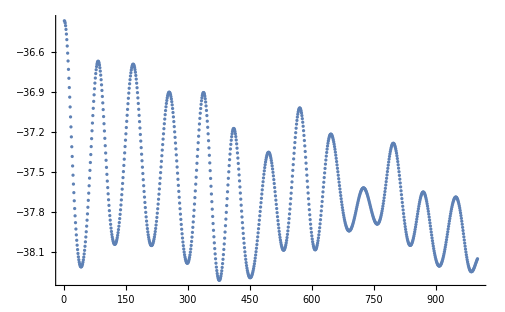

```mathematica
ListPlot[energy,PlotRange->All]
```

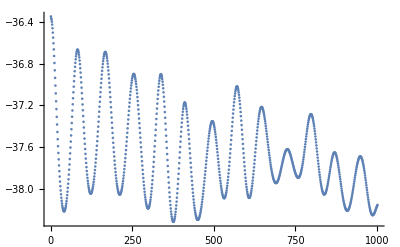

```mathematica
ListPlot[energy+kinetic,PlotRange->All]
```

```mathematica
averageKE=Sum[ dt kinetic[[i]],{i,1,timesteps/2}]/Sum[dt,{i,1,timesteps/2}]
```

0.0000256362

```mathematica
Clear[T]
```

```mathematica
First[Solve[averageKE==3/2 natoms kb T,T]]
```

{T→(1.31468×10^-6)/kb}